```mathematica
means = Import["mean", "Table", Path->NotebookDirectory[]];
withFeatures = Flatten[Select[means, #[[2]] == 1&] [[All,1]]];
withoutFeatures = Flatten[Select[means, #[[2]] == 0&] [[All,1]]];
Mean[withFeatures]
StandardDeviation[withFeatures]
Mean[withoutFeatures]
StandardDeviation[withoutFeatures]
```

1.12461×10^-14

1.15904×10^-14

1.19551×10^-15

3.51867×10^-15

```mathematica
Length[means]
Length[withoutFeatures]
q = Quantile[withFeatures,0.05]
selected = Select[means, #[[1]] < q &][[All,1]];
Length[selected]
Length[Intersection[selected, withoutFeatures]]
```

115495

56659

4.65312×10^-16

44663

41629

```mathematica
Length[Select[withoutFeatures, # > q &]] / Length@withoutFeatures
```

14937/56659

```mathematica
N[14937/56659]
```

0.26363

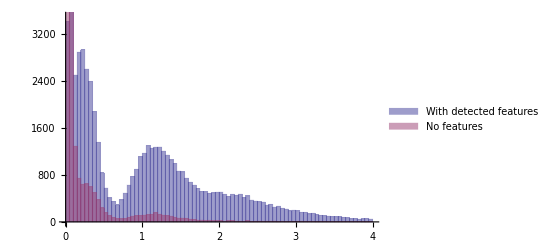

```mathematica
Histogram[{Select[withFeatures,# < 4*10^(-14)&],Select[withoutFeatures,# < 4*10^(-14)&]}, PlotRange->{0,3500},BaseStyle->{FontSize->17},ChartLegends->Placed[{"With detected features","No features"},Center]]
```

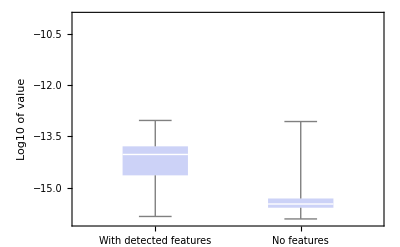

4.65312×10^-16

4.8337×10^-15

```mathematica
meansBoxPlot = BoxWhiskerChart[{Log10[withFeatures], Log10[withoutFeatures]},ChartLabels->{"With detected features","No features"},FrameLabel->{None, "Log10 of value"},BaseStyle->
{FontSize->18},ImageSize->{400,300}, PlotRange->{-16,-10}]
Quantile[withFeatures,0.05]
Quantile[withoutFeatures,0.95]
```

```mathematica
sds=Import["sd","Table",Path->NotebookDirectory[]];
sdWithFeatures=Flatten[Select[sds,#1⟦2⟧==1&]⟦All,1⟧];
sdWithoutFeatures=Flatten[Select[sds,#1⟦2⟧==0&]⟦All,1⟧];
Mean[sdWithFeatures]
StandardDeviation[sdWithFeatures]
Mean[sdWithoutFeatures]
StandardDeviation[sdWithoutFeatures]
```

8.2218×10^-14

1.00743×10^-13

8.51896×10^-15

2.66199×10^-14

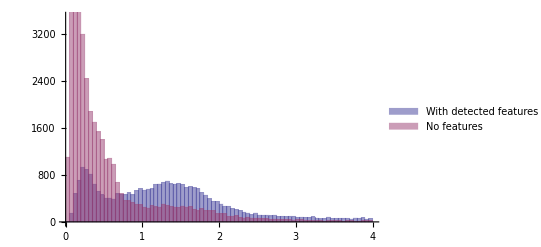

```mathematica
Histogram[{Select[sdWithFeatures,# < 4*10^(-14)&],Select[sdWithoutFeatures,# < 4*10^(-14)&]}, PlotRange->{0,3500},BaseStyle->{FontSize->17},ChartLegends->Placed[{"With detected features","No features"},Center]]
```

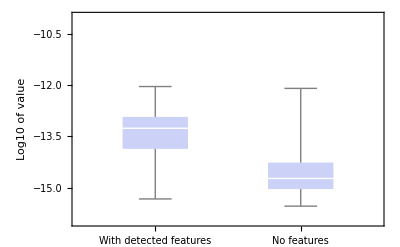

```mathematica
sdBoxPlot = BoxWhiskerChart[{Log10[sdWithFeatures], Log10[sdWithoutFeatures]},ChartLabels->{"With detected features","No features"},FrameLabel->{None, "Log10 of value"},BaseStyle->
{FontSize->18},ImageSize->{400,300}, PlotRange->{-16,-10}]
```

```mathematica
maxs=Import["max","Table",Path->NotebookDirectory[]];
maxWithFeatures=Flatten[Select[maxs,#1⟦2⟧==1&]⟦All,1⟧];
maxWithoutFeatures=Flatten[Select[maxs,#1⟦2⟧==0&]⟦All,1⟧];
Mean[maxWithFeatures]
StandardDeviation[maxWithFeatures]
Mean[maxWithoutFeatures]
StandardDeviation[maxWithoutFeatures]
```

2.0554×10^-12

2.5891×10^-12

3.16212×10^-13

7.2515×10^-13

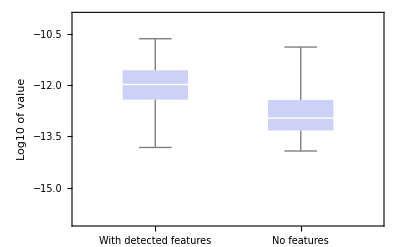

9.64505×10^-14

1.08525×10^-12

```mathematica
maxBoxPlot = BoxWhiskerChart[{Log10[maxWithFeatures], Log10[maxWithoutFeatures]},ChartLabels->{"With detected features","No features"},FrameLabel->{None, "Log10 of value"},BaseStyle->
{FontSize->18},ImageSize->{400,300}, PlotRange->{-16,-10}]
Quantile[maxWithFeatures,0.05]
Quantile[maxWithoutFeatures,0.95]
```

```mathematica
Max[{maxWithFeatures, maxWithoutFeatures}]
```

2.23569×10^-11

```mathematica
GraphicsGrid[{{Labeled[meansBoxPlot,"Means"], Labeled[sdBoxPlot,"Std. deviations"]}, {Labeled[maxBoxPlot,"Maximum values"]}},
BaseStyle->{FontSize->18}]
```

-Graphics-

```mathematica
trace=Log10[Import["trace","Table",Path->NotebookDirectory[]][[All,2]]];
```

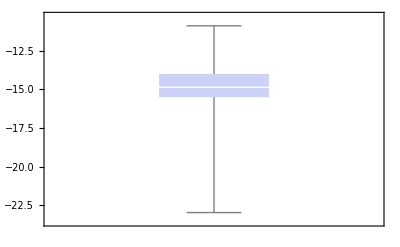

```mathematica
BoxWhiskerChart[trace]
```

```mathematica
feat=Import["features","Table",Path->NotebookDirectory[]][[All,2;;3]];
```

```mathematica
features = Log10@Select[feat, #[[2]]≠"noFeature" &][[All,1]];
noFeatures = Log10@Select[feat, #[[2]]=="noFeature" &][[All,1]];
```

```mathematica
Length[features]
Length[noFeatures]
```

825852

824212

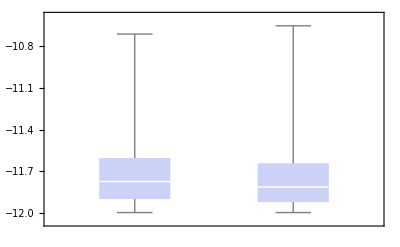

```mathematica
BoxWhiskerChart[{features, noFeatures}]
```